### Make dividers bigger and decrease line spacing

```mathematica
rowsizes = <|50-> 40, 12-> 50,106->30, 100->40 |>;
```

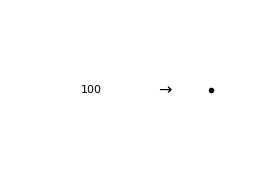
-Graphics--Graphics--Graphics--Graphics--Graphics-

```mathematica
Row[KeyValueMap[
Function[{key, val},
GraphicsRow[{#[[1]], Style["→", 16], #[[2]]}]&[Labeled[CellularAutomatonHistoryPlot["GameOfLife",{$LifeData[key]["MatrixData"],0},$LifeData[key]["Period"],ImageSize->22.5(Times@@Dimensions[$LifeData[key]["MatrixData"]] )^(1/4), MeshStyle->Opacity[(.5/(Times@@Dimensions[$LifeData[key]["MatrixData"]])^.35)]],Style[#, 12]&@Text[ToString[$LifeData[key]["Period"]]],Bottom]->
GraphicsRow[(
Labeled[CellularAutomatonHistoryPlot["GameOfLife",{$LifeData[#1]["MatrixData"],0},$LifeData[#1]["Period"],ImageSize->{Automatic, rowsizes[$LifeData[key]["Period"]]}(*20(Times@@Dimensions[$LifeData[#1]["MatrixData"]] )^(1/4)*)],Style[Text[ToString[$LifeData[#1]["Period"]]], 11], Bottom]&/@val)]]],Take[ReverseSortBy[Union[DeleteCases[#,None]]&/@oresall,Length],4]], Graphics[Style[Line[{{0,-1},{0,1}}],GrayLevel[.4]],PlotRange->{{-.1,.1},{-1,1}},ImageSize->{12,60}]]
```

```mathematica
Style[Row[KeyValueMap[
Function[{key, val},
GraphicsRow[{#[[1]], Style["→", 16], #[[2]]}]&[Labeled[CellularAutomatonHistoryPlot["GameOfLife",{$LifeData[key]["MatrixData"],0},$LifeData[key]["Period"],ImageSize->22.5(Times@@Dimensions[$LifeData[key]["MatrixData"]] )^(1/4), MeshStyle->Opacity[(.5/(Times@@Dimensions[$LifeData[key]["MatrixData"]])^.35)]],Style[#, 12]&@Text[ToString[$LifeData[key]["Period"]]],Bottom]->
GraphicsRow[(
Labeled[CellularAutomatonHistoryPlot["GameOfLife",{$LifeData[#1]["MatrixData"],0},$LifeData[#1]["Period"],ImageSize->{Automatic, rowsizes[$LifeData[key]["Period"]]}(*20(Times@@Dimensions[$LifeData[#1]["MatrixData"]] )^(1/4)*)],Style[Text[ToString[$LifeData[#1]["Period"]]], 11], Bottom]&/@val)]]],Take[ReverseSortBy[Union[DeleteCases[#,None]]&/@oresall,Length],4]], Graphics[Style[Line[{{0,-2},{0,2}}],GrayLevel[.4]],PlotRange->{{-.1,.1},{-1,1}},ImageSize->{12,100}]], LineSpacing->{1, 15}]
```

-Graphics--Graphics--Graphics--Graphics--Graphics-

### Remove chucklebait

Fixed:

```mathematica
oresall = ;
```

```mathematica
With[{d=Total[KeyDrop[Counts[Flatten[Values[Association[oresall]]]],None]]},ListLogLogPlot[Join[KeyValueMap[Callout[#2/d,Labeled[ArrayPlot[ArrayPad[$LifeData[#1]["MatrixData"],1],ImageSize->{UpTo[25],25}],$LifeData[#1]["Period"]]]&,#1],Values[#2/d]]&@@(Delete[#, Key["Chucklebait"]]&/@TakeDrop[ReverseSort[KeyDrop[Counts[Flatten[Values[Association[oresall]]]],None]],20]),Frame->True,FrameTicks->{Automatic, {Table[i,{i, Join[Range[10], {20, 30, 40, 50}]}], Automatic}},AspectRatio->.4,ImageSize->650,FrameLabel->{"rank","frequency"},PlotStyle->PointSize[.01]]]
```

-Graphics-

### Find the derivation of xresall, and include it...

Normalizing by the number of new patterns found each year, we see a general gradual increase in the relative number of new modular parts, presumably reflecting the greater use of search in finding patterns, or components of patterns:

Find the derivation of xresall, and include it...

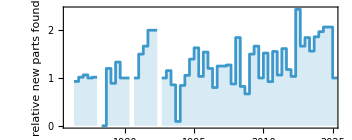

```mathematica
ListStepPlot[KeySort[KeyValueMap[#1->Quiet[#2/Count[#Year&/@ $LifeData,#1]]&,KeySort[Merge[{Total/@Map[Last,GroupBy[KeyValueMap[{$LifeData[#1]["Year"],Count[#2,None]}&,xresall],First],{2}],Association[Table[y->0,{y,1969,2025}]]},Max]]]],AspectRatio->.4,Frame->True,Filling->Axis,FrameLabel->{None,"relative new parts found"},PlotRange->All]
```

```mathematica
xresall=Association[ParallelMap[#->MemoryConstrained[(PatternCheck[#,allprims]&/@Union[CanonicalParts[Normal[$LifeData[#]["MatrixData"]]]]),10^7]&,Keys[Select[Select[$LifeData,KeyExistsQ[#,"InitialWeight"]&&KeyExistsQ[#,"MatrixData"]&],#InitialWeight<4000&&(Times@@Dimensions[#MatrixData])<4000&]]]/.(x_->{x_}):>(x->{None})];
```

```mathematica
ListStepPlot[KeySort[KeyValueMap[#1->Quiet[#2/Count[#Year&/@ $LifeData,#1]]&,KeySort[Merge[{Total/@Map[Last,GroupBy[KeyValueMap[{$LifeData[#1]["Year"],Count[#2,None]}&,xresall],First],{2}],Association[Table[y->0,{y,1969,2025}]]},Max]]]],AspectRatio->.4,Frame->True,Filling->Axis,FrameLabel->{None,"relative new parts found"},PlotRange->All]
```

-Graphics-

### Label each number of modular parts. 1, ≤5 ,

How has this changed over time?  This shows a cumulative plot of the relative frequencies with which different numbers of modular parts appear in patterns up to a given year

Label each number of modular parts

1, ≤5 ,

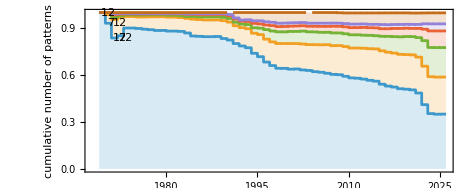

```mathematica
With[{norm=Association[Thread[Range[1969,2025]->Accumulate[Table[Count[Values[#Year&/@$LifeData],y],{y,1969,2025}]]]]},ListStepPlot[MapThread[Labeled[#1,#2,Right]&,{Map[{#[[1]],#[[2]]/norm[#[[1]]]}&,FoldList[{#2[[1]],#1[[2]]+#2[[2]]}&,#]&/@Transpose[KeyValueMap[{x,y}|->{x,#}&/@y,BinCounts[#,{Flatten[{1,Range[2,25,5],Infinity}]}]&/@KeySort[partsbydate]]],{2}],Flatten[{1,Range[2,25,5]}]}],PlotLayout->"Stacked",Filling->Table[i->If[i==1,Axis,{i-1}],{i,1,24}],Frame->True,AspectRatio->.4,(*PlotStyle->{Red,Automatic},*)FrameLabel->{None,"cumulative number of patterns"},PlotRange->{0,1}]]
```

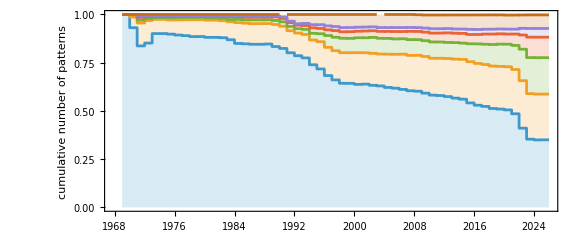

```mathematica
With[{norm=Association[Thread[Range[1969,2025]->Accumulate[Table[Count[Values[#Year&/@$LifeData],y],{y,1969,2025}]]]]},ListStepPlot[MapThread[#1&,{Map[{#[[1]],#[[2]]/norm[#[[1]]]}&,FoldList[{#2[[1]],#1[[2]]+#2[[2]]}&,#]&/@Transpose[KeyValueMap[{x,y}|->{x,#}&/@y,BinCounts[#,{Flatten[{1,Range[2,25,5],Infinity}]}]&/@KeySort[partsbydate]]],{2}],Flatten[{1,Range[2,25,5]}]}],PlotLayout->"Stacked",Filling->Table[i->If[i==1,Axis,{i-1}],{i,1,24}],Frame->True,AspectRatio->.4,(*PlotStyle->{Red,Automatic},*)FrameLabel->{None,"cumulative number of patterns"},PlotRange->{0,1}, FrameTicks->{{Automatic, Transpose[Reverse@{Text/@{"1","≤5", "≤10", "≤15", "≤20", ">20"},{.35, .58, .775, .875, .925, 1}}]}, Automatic}]]
```

### Make RHS images cut off the gliders at the right, and be taller, etc...

So by picking the separation n to be large enough, we can make this configuration “live as long as we want”.  But what if we limit the size of the initial pattern, say to 32×32?  In 2022 the following pattern was constructed:

Make RHS images cut off the gliders at the right, and be taller
Add space between image blocks

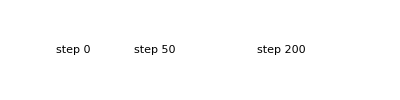
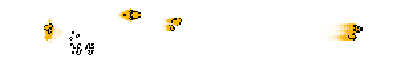
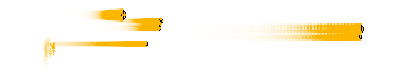
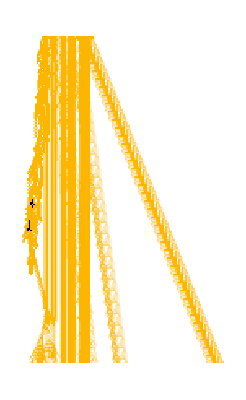
-Graphics-
-Graphics-step 500
-Graphics-step 2000-Graphics-

```mathematica
Row[{Column[{GraphicsRow[Labeled[CellularAutomatonHistoryPlot["GameOfLife",{SparseArray[…],0},#,Mesh->None,ImageSize->{Automatic,80},"Decay"->.9],Text[Style[StringTemplate["step ``"][#],10]]]&/@{0,50,200},ImageSize->{400,Automatic}],Labeled[CellularAutomatonHistoryPlot["GameOfLife",{SparseArray[…],0},#,Mesh->None,ImageSize->{400,Automatic},"Decay"->.9],Text[Style[StringTemplate["step ``"][#],10]]]&[500],Labeled[CellularAutomatonHistoryPlot["GameOfLife",{SparseArray[…],0},#,Mesh->None,ImageSize->{400,Automatic},"Decay"->.993],Text[Style[StringTemplate["step ``"][#],10]]]&[2000]}],GraphicsRow[{CellularAutomatonPlot3D["GameOfLife",{SparseArray[…],0},200,Mesh->None],CellularAutomatonSpacetimePlot["GameOfLife",{SparseArray[…],0},200,Mesh->None,"Decay"->.95]}]}]
```

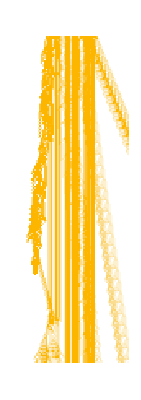
-Graphics-
-Graphics-step 500
-Graphics-step 2000-Graphics-

```mathematica
Row[{Column[{GraphicsRow[Labeled[CellularAutomatonHistoryPlot["GameOfLife",{SparseArray[…],0},#,Mesh->None,ImageSize->{Automatic,80},"Decay"->.9],Text[Style[StringTemplate["step ``"][#],10]]]&/@{0,50,200},ImageSize->{400,Automatic}],Labeled[CellularAutomatonHistoryPlot["GameOfLife",{SparseArray[…],0},#,Mesh->None,ImageSize->{400,Automatic},"Decay"->.9],Text[Style[StringTemplate["step ``"][#],10]]]&[500],Labeled[CellularAutomatonHistoryPlot["GameOfLife",{SparseArray[…],0},#,Mesh->None,ImageSize->{400,Automatic},"Decay"->.993],Text[Style[StringTemplate["step ``"][#],10]]]&[2000]}],GraphicsRow[{CellularAutomatonPlot3D["GameOfLife",{SparseArray[…],0},{200, {-20, 50}, {-20, 50}},Mesh->None, ImageSize->Medium],CellularAutomatonSpacetimePlot["GameOfLife",{SparseArray[…],0},{200, {-20, 50}, {-20, 50}},Mesh->None,"Decay"->.95]}, ImageSize->{Automatic, 290}]}]
```

### Fix crashing. If necessary remove some examples.

And here are some other outcomes from adaptive evolution:

Fix crashing
If necessary remove some examples

```mathematica
aares=ParallelTable[(SeedRandom[34578+i];With[{max=400},Nest[Module[{u=MapAt[1-#&,#[[1]],RandomInteger[{1,16},2]],lt},lt=TestCALifeTime[CellularAutomaton["GameOfLife",{u,0},max]];If[lt>0&&lt>=#[[2]],{u,lt},#]]&,{RandomInteger[1,{16,16}],0},2000]]),{i,200}];
```

```mathematica
CloudExport[aares,"WXF",Permissions->"Public"]
```

CloudObject[https://www.wolframcloud.com/obj/2f6183db-0aea-47a2-8f81-f7d4df6449b2]

```mathematica
Import["https://www.wolframcloud.com/obj/2f6183db-0aea-47a2-8f81-f7d4df6449b2"];
```

```mathematica
aares = ;
```

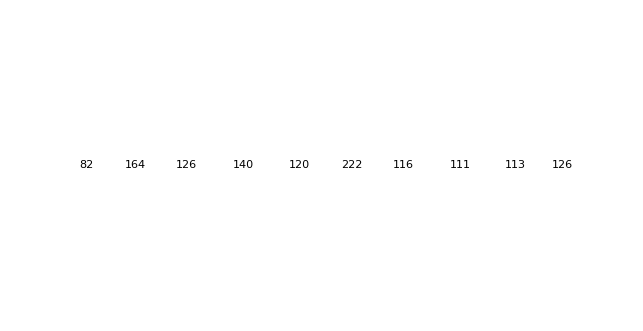

```mathematica
GraphicsRow[Labeled[CellularAutomatonPlot3D["GameOfLife",{#[[1]],0},1+#[[2]],ImageSize->{Automatic,20Sqrt[#[[2]]+4]}],Text[#[[2]]]]&/@aares[[{14,165,101,194,112,87,65,47,30,33}]]]
```

Smaller center seems okay

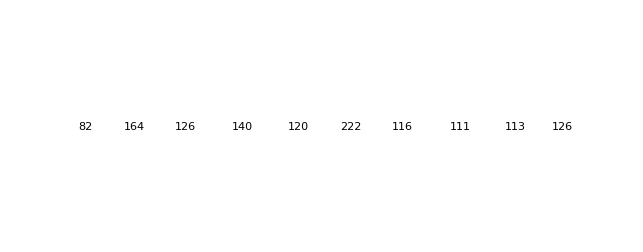

```mathematica
GraphicsRow[Labeled[CellularAutomatonPlot3D["GameOfLife",{#[[1]],0},1+#[[2]],ImageSize->{Automatic,15Sqrt[#[[2]]+4]}],Text[#[[2]]]]&/@aares[[{14,165,101,194,112,87,65,47,30,33}]]]
```

Aligned with labels at top

```mathematica
GraphicsRow[Rasterize@Labeled[CellularAutomatonPlot3D["GameOfLife",{#[[1]],0},1+#[[2]],ImageSize->{Automatic,15Sqrt[#[[2]]+4]}],Style[Text[#[[2]]], 10], Top]&/@aares[[{14,165,101,194,112,87,65,47,30,33}]], Alignment->Top, ImageSize->{650, Automatic}, Spacings->{Automatic, {0, 0}}]
```

-Graphics-

Aligned with labels at the bottom

```mathematica
GraphicsRow[Rasterize@Labeled[CellularAutomatonPlot3D["GameOfLife",{#[[1]],0},1+#[[2]],ImageSize->{Automatic,15Sqrt[#[[2]]+4]}],Style[Text[#[[2]]], 10], Bottom]&/@aares[[{14,165,101,194,112,87,65,47,30,33}]], Alignment->Bottom, ImageSize->{650, Automatic}, Spacings->{Automatic, {0, 0}}]
```

### Fix silly spacing issues

Now insert two R pentominoes.  They’ll start doing their thing, generating what seems like quite random behavior.  But the “cage” defined by the “eaters” limits what can happen, and in the end what emerges is an oscillator---that has period 129:

Fix silly spacing issues

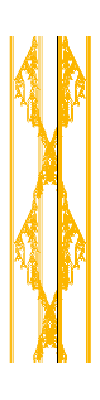

```mathematica
GraphicsRow[{GraphicsGrid[Partition[Table[CellularAutomatonHistoryPlot["GameOfLife",{$LifeData["p129 R-pentomino hassler"]["MatrixData"],0},43*n,Mesh->None,"Decay"->.95],{n,0,3}],2], Spacings->{5, 5}],CellularAutomatonPlot3D["GameOfLife",{$LifeData["p129 R-pentomino hassler"]["MatrixData"],0},129*2,ViewPoint->{0.7216886031517927,-2.919410267958318,1.5511960699474316}],CellularAutomatonSpacetimePlot["GameOfLife",{$LifeData["p129 R-pentomino hassler"]["MatrixData"],0},129*2,Mesh->None,"Decay"->.95]}]
```

### BarChartify stepplots

```mathematica
ListStepPlot[KeySort[KeyValueMap[#1->Quiet[#2/Count[#Year&/@ $LifeData,#1]]&,KeySort[Merge[{Total/@Map[Last,GroupBy[KeyValueMap[{$LifeData[#1]["Year"],Count[#2,None]}&,xresall],First],{2}],Association[Table[y->0,{y,1969,2025}]]},Max]]]],AspectRatio->.4,Frame->True,Filling->Axis,FrameLabel->{None,"relative new parts found"},PlotRange->All]
```

-Graphics-

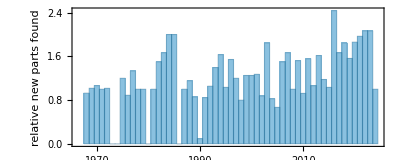

```mathematica
BarChart[ReplaceAll[KeySort[KeyValueMap[#1->Quiet[#2/Count[#Year&/@ $LifeData,#1]]&,KeySort[Merge[{Total/@Map[Last,GroupBy[KeyValueMap[{$LifeData[#1]["Year"],Count[#2,None]}&,xresall],First],{2}],Association[Table[y->0,{y,1969,2025}]]},Max]]]],Indeterminate->0],Frame->True,FrameTicks->{Automatic, {Table[{i, i + 1967},{i, 3, 57, 10}], Automatic}}, ChartStyle->Directive[Opacity[.6,ColorData["DefaultPlotColors"][1]],EdgeForm[Darker[ColorData["DefaultPlotColors"][1]]]], AspectRatio->.4,FrameLabel->{None,"relative new parts found"},PlotRange->All]
```

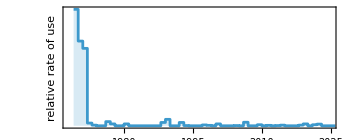

```mathematica
ListStepPlot[With[{o=$LifeData[#]["Year"]&/@DeleteCases[Flatten[Values[resall]],None]},Table[{y,Count[o,y]},{y,1969,2025}]],Filling->Axis,Frame->True,AspectRatio->.4,PlotRange->All,FrameLabel->{None,"relative rate of use"},FrameTicks->{{None,None},{Automatic,None}}]
```

```mathematica
With[{o=$LifeData[#]["Year"]&/@DeleteCases[Flatten[Values[resall]],None]},Table[{y,Count[o,y]},{y,1969,2025}]]
```

{{1969,561},{1970,408},{1971,373},{1972,13},{1973,3},{1974,0},{1975,0},{1976,20},{1977,9},{1978,0},{1979,0},{1980,9},{1981,0},{1982,0},{1983,0},{1984,0},{1985,0},{1986,0},{1987,0},{1988,16},{1989,31},{1990,0},{1991,0},{1992,16},{1993,1},{1994,0},{1995,0},{1996,0},{1997,4},{1998,2},{1999,0},{2000,9},{2001,0},{2002,0},{2003,0},{2004,1},{2005,0},{2006,17},{2007,0},{2008,0},{2009,5},{2010,0},{2011,2},{2012,0},{2013,1},{2014,3},{2015,0},{2016,0},{2017,0},{2018,3},{2019,9},{2020,0},{2021,5},{2022,8},{2023,0},{2024,0},{2025,0}}

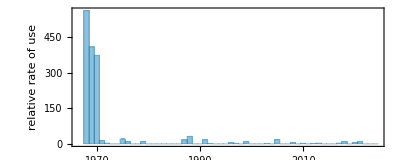

```mathematica
BarChart[With[{o=$LifeData[#]["Year"]&/@DeleteCases[Flatten[Values[resall]],None]},Table[{y,Count[o,y]},{y,1969,2025}]][[All, 2]],Frame->True,FrameTicks->{Automatic, {Table[{i, i + 1967},{i, 3, 57, 10}], Automatic}}, ChartStyle->Directive[Opacity[.6,ColorData["DefaultPlotColors"][1]],EdgeForm[Darker[ColorData["DefaultPlotColors"][1]]]], AspectRatio->.4,FrameLabel->{None,"relative rate of use"},PlotRange->All]
```

### Remove 0 from activity chart

Drop a line from the frame tick to to the year the structure was first discovered

Get rid of the 0 on the rank scale ... as well as the space at the beginning

```mathematica
resall = ;
```

```mathematica
activity = Module[{rrr, xr},
rrr=Association[DeleteCases[Union[#],None]&/@Association[resall]];
xr=Flatten[KeyValueMap[Thread[#2->$LifeData[#1]["Year"]]&,Association[rrr]]];
#->Cases[xr,(#->x_)->x]&/@Keys[Take[ReverseSort[Counts[Flatten[Values[rrr]]]],32]]];
```

```mathematica
fcef[{{xmin_,xmax_},{ymin_,ymax_}},v_,meta_,style___]:={Rectangle[{xmin,ymin},{xmax,ymax}]}
```

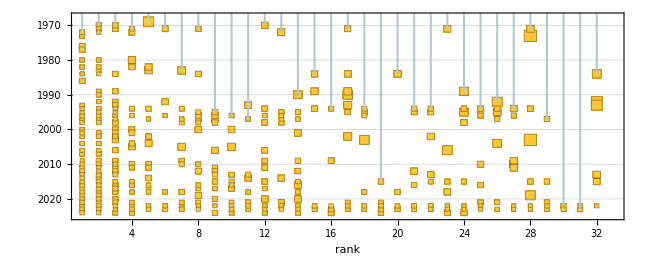

```mathematica
With[{totsyear=KeySort[Merge[Values[Counts/@Take[Association[activity],32]],Total]],totsitem=Total/@Values[Counts/@Take[Association[activity],32]]},BubbleChart[Catenate[MapIndexed[Function[{assoc,idx},KeyValueMap[{First@idx,#1,(#2/totsyear[#1])/totsitem[[First@idx]]}&,assoc]],Values[Counts/@Take[Association[activity],32]]]],ChartElementFunction->fcef,ScalingFunctions->{Automatic,"Reverse"},PlotRange->{{1,33},Automatic},PlotRangePadding->{{.5,None},{Automatic,Automatic}},AspectRatio->.4,GridLines->{None,Range[1970,2020,10]},BubbleScale->"Area",BubbleSizes->{.02,.06},FrameTicks->{{Automatic,Automatic},Reverse[{Transpose[{Range[1,32,1],CellularAutomatonHistoryPlot["GameOfLife",{$LifeData[#]["MatrixData"],0},0,ImageSize->{20,20},Mesh->None,MeshStyle->Opacity[.05]]&/@Keys[Take[Association[activity],32]]}],Automatic}]},ImageSize->650,FrameLabel->{"rank",None},
Epilog->{Hue[0.55, 0.14, 0.8200000000000001],AbsoluteThickness[1.5],MapIndexed[Line[{ {First@#2, 0},{First@#2,-#1}}]&, activity[[All, 2, 1]]],
Red,PointSize[.1], Point[{10, 10}]
}, PerformanceGoal->"Speed"
]]
```

### Legend bfhs, (Should I make these bar charts too?)

Check for zeros

Put on legend:
[ blue ] with previously found parts
[ red ] no previously found parts

For Developer

```mathematica
dat=KeyValueMap[{x,y}|->{x,#}&/@y,{Count[#,True],Count[#,False]}&/@KeySort[Merge[{Map[Last,GroupBy[KeyValueMap[{$LifeData[#1]["Year"],Union[#2]==={None}}&,xresall],First],{2}],Association[Table[y->{},{y,1969,2025}]]},Apply[Join]]]];
```

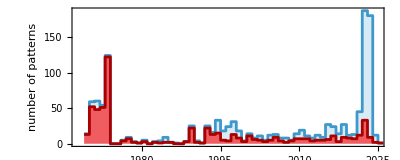

```mathematica
Show[{
ListStepPlot[{#[[1,1]],Total[#[[All,2]]]}&/@dat,Filling->Axis,Frame->True,PlotRange->All,AspectRatio->.4,
PlotStyle->ColorData["DefaultPlotColors"][1],FrameLabel->{None,"number of patterns"}],
ListStepPlot[dat[[All,1]],Filling->Axis,Frame->True,PlotRange->All,AspectRatio->.4,
PlotStyle->Darker[Red],FillingStyle->Opacity[.6,Red]]}]
```

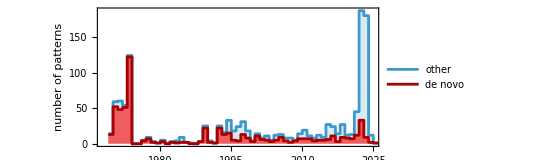

```mathematica
Show[{
ListStepPlot[{#[[1,1]],Total[#[[All,2]]]}&/@dat,Filling->Axis,Frame->True,PlotRange->All,AspectRatio->.4,
PlotStyle->ColorData["DefaultPlotColors"][1],FrameLabel->{None,"number of patterns"}, PlotLegends->{"other"}],
ListStepPlot[dat[[All,1]],Filling->Axis,Frame->True,PlotRange->All,AspectRatio->.4,
PlotStyle->Darker[Red],FillingStyle->Opacity[.6,Red], PlotLegends->{"de novo"}]} ]
```

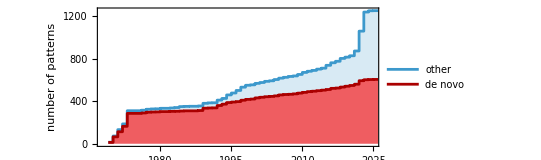

```mathematica
dat=FoldList[{#2[[1]],#1[[2]]+#2[[2]]}&,#]&/@Transpose[KeyValueMap[{x,y}|->{x,#}&/@y,{Count[#,True],Count[#,False]}&/@KeySort[Merge[{Map[Last,GroupBy[KeyValueMap[{$LifeData[#1]["Year"],Union[#2]==={None}}&,xresall],First],{2}],Association[Table[y->{},{y,1969,2025}]]},Apply[Join]]]]];

Show[{
ListStepPlot[Transpose[{dat[[1,All,1]],Total[dat[[All,All,2]]]}],Filling->Axis,Frame->True,PlotRange->All,AspectRatio->.4,
PlotStyle->ColorData["DefaultPlotColors"][1],FrameLabel->{None,"number of patterns"} ,PlotLegends->{"other"}],
ListStepPlot[dat[[1]],Filling->Axis,Frame->True,PlotRange->All,AspectRatio->.4,
PlotStyle->Darker[Red],FillingStyle->Opacity[.6,Red], PlotLegends->{"de novo"}]
}]
```

### Put better meshstyle into the other bounding box history plot combo

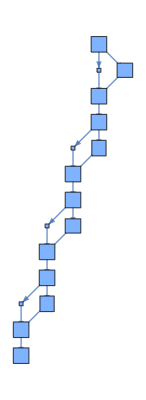
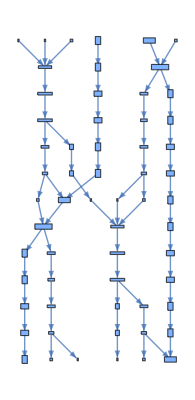
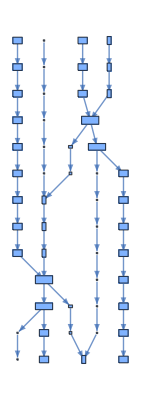
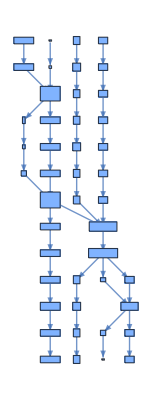
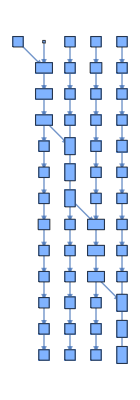
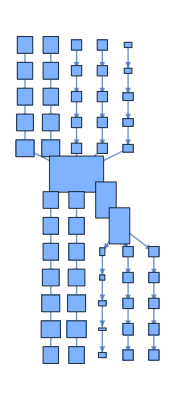
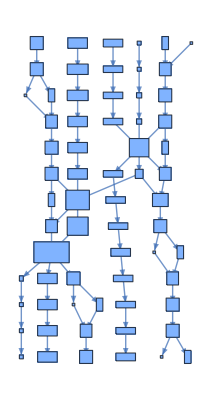
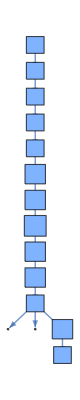
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
1972 | 1984 | 1989 | 1994 | 1995 | 1995 | 2004 | 2009-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
2015 | 2019 | 2021 | 2022 | 2022 | 2023 | 2023

```mathematica
Style[Row[With[{elems=With[{data=Quiet[Append[Append[KeyDrop[Select[$LifeData,#["Class"]==="Oscillator"&&#["Period"]==12&],"p12rpentominohasslers"],Module[{u=$LifeData["p12rpentominohasslers"]},u["Name"]="new1";u["MatrixData"]=SparseArray[Select[Most[ArrayRules[$LifeData["p12rpentominohasslers"]["MatrixData"]]],#[[1,2]]<30&]];"new1"->u]],Module[{u=$LifeData["p12rpentominohasslers"]},u["Name"]="new2";u["MatrixData"]=SparseArray[Select[Most[ArrayRules[$LifeData["p12rpentominohasslers"]["MatrixData"]]],#[[1,2]]>52&]];"new2"->u]]]},Values[{Graph[BoundingBoxLayeredGraph[#],ImageSize->{Automatic,150}],CellularAutomatonHistoryPlot["GameOfLife",{#MatrixData,0},16,ImageSize->13Sqrt[Reverse@Dimensions[#MatrixData]]],Text[Style[#Year,Small,Gray]]}&/@SortBy[data//Quiet,#Year&]]]},Grid[Transpose[#],Dividers->{All,False},FrameStyle->GrayLevel[.7],Alignment->Center]&/@Partition[elems,UpTo[8]]]],LineSpacing->{1,40}]
```

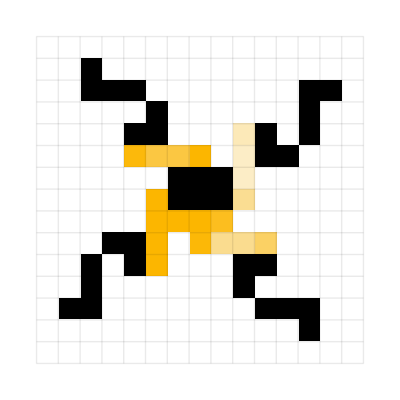
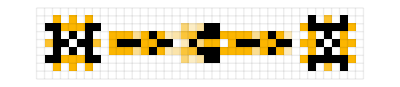
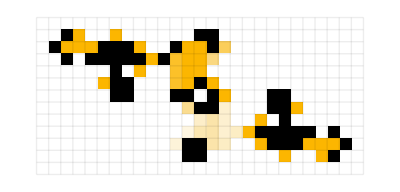
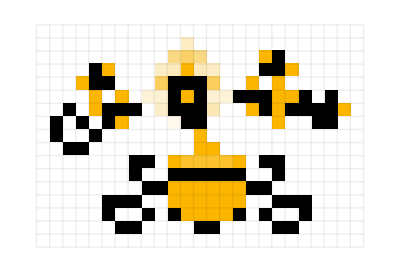
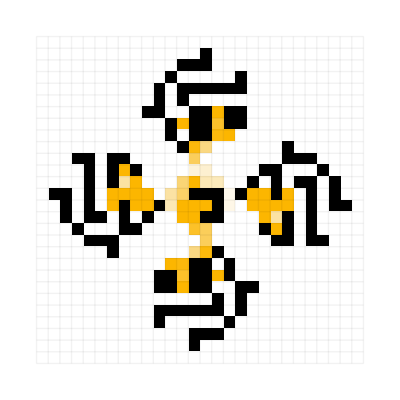
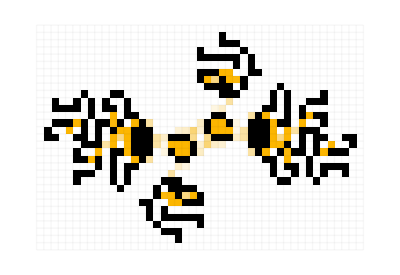
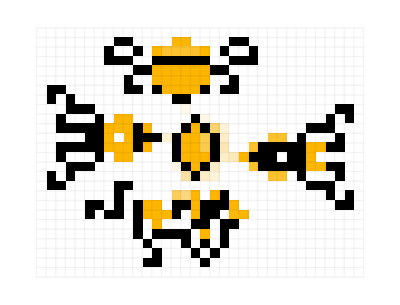
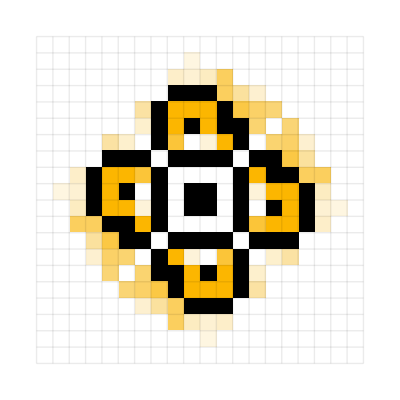
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
1972 | 1984 | 1989 | 1994 | 1995 | 1995 | 2004 | 2009-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
2015 | 2019 | 2021 | 2022 | 2022 | 2023 | 2023

```mathematica
Style[Row[With[{elems=With[{data=Quiet[Append[Append[KeyDrop[Select[$LifeData,#["Class"]==="Oscillator"&&#["Period"]==12&],"p12rpentominohasslers"],Module[{u=$LifeData["p12rpentominohasslers"]},u["Name"]="new1";u["MatrixData"]=SparseArray[Select[Most[ArrayRules[$LifeData["p12rpentominohasslers"]["MatrixData"]]],#[[1,2]]<30&]];"new1"->u]],Module[{u=$LifeData["p12rpentominohasslers"]},u["Name"]="new2";u["MatrixData"]=SparseArray[Select[Most[ArrayRules[$LifeData["p12rpentominohasslers"]["MatrixData"]]],#[[1,2]]>52&]];"new2"->u]]]},Values[{Graph[BoundingBoxLayeredGraph[#],ImageSize->{Automatic,150}],CellularAutomatonHistoryPlot["GameOfLife",{#MatrixData,0},16,ImageSize->13Sqrt[Reverse@Dimensions[#MatrixData]], MeshStyle->Opacity[(.5/(Times@@Dimensions[#MatrixData])^.35)]],Text[Style[#Year,Small,Gray]]}&/@SortBy[data//Quiet,#Year&]]]},Grid[Transpose[#],Dividers->{All,False},FrameStyle->GrayLevel[.7],Alignment->Center]&/@Partition[elems,UpTo[8]]]],LineSpacing->{1,40}]
```

### remove braces

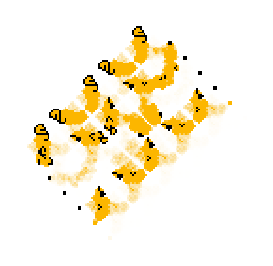
{-Graphics-,-Graphics-}

```mathematica
{CellularAutomatonHistoryPlot["GameOfLife",{$LifeData["13-engine Cordership"]["MatrixData"],0},96 2,"Decay"->.95,Mesh->None],CellularAutomatonSpacetimePlot["GameOfLife",{Reverse/@$LifeData["13-engine Cordership"]["MatrixData"],0},96 4,Mesh->None,"Decay"->.97]}
```

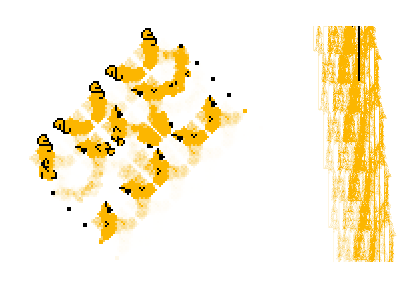

```mathematica
GraphicsRow[{CellularAutomatonHistoryPlot["GameOfLife",{$LifeData["13-engine Cordership"]["MatrixData"],0},96 2,"Decay"->.95,Mesh->None, ImageSize->{Automatic, 275}],CellularAutomatonSpacetimePlot["GameOfLife",{Reverse/@$LifeData["13-engine Cordership"]["MatrixData"],0},96 4,Mesh->None,"Decay"->.97, ImageSize->{Automatic, 275}]}]
```

### Show multiple panels of slices Maybe only use 3D if that’s what’s done in the previous example

Rotate these to the correct direction

For Developer

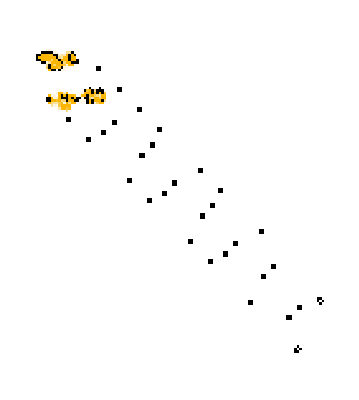
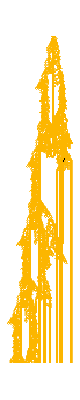
{-Graphics-,-Graphics-,-Graphics3D-}

```mathematica
{CellularAutomatonHistoryPlot["GameOfLife",{Transpose@SparseArray[…],0},1100,Mesh->False],CellularAutomatonSpacetimePlot["GameOfLife",{Transpose@SparseArray[…],0},400,Mesh->None,"Decay"->.99],CellularAutomatonPlot3D["GameOfLife",{SparseArray[…],0},200]}
```